Gauss’s area formula,  surveyor’s formula, the shoelace formula. 

See https://en.wikipedia.org/wiki/Shoelace_formula

This is the centroid of a list of points, as well as the sheet containing them (same by scaling symmetry for a convex body; by induction on polygonal non-convex bodies)

```mathematica
centroid[a_/;(Length[a]>=3 && (And@@(Length[#]==2&/@a)))]:=
Plus@@(Table[(a[[i]]+a[[Mod[i,Length[a]]+1]])Det[{a[[i]],a[[Mod[i,Length[a]]+1]]}],{i,Length[a]}])/3/(Plus@@Table[Det[{a[[i]],a[[Mod[i,Length[a]]+1]]}],{i,Length[a]}])

drawcentroid:=Graphics[{Line[Append[#,#[[1]]]],Disk[#,.1]&/@#,Disk[centroid[#],.2]}]&
```

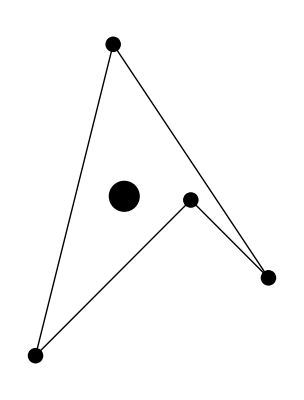

```mathematica
drawcentroid@{{1,1},{2,5},{4,2},{3,3}}
```